# Exercícios computacionais 2: Autômatos Celulares

## 1. Verifique a documentação da função CellularAutomaton (e o tutorial relativo a Cellular Automata), observando suas parametrizações possíveis. Em particular, entenda a equivalência entre as seguintes formas:

Boolean functions: (e.g., rule 90 as a pure Boolean function: Xor[#1,#3]& , or simply as BooleanFunction[90,3])

```mathematica
ca1=CellularAutomaton[BooleanFunction[90,3],{{1},0},5]
ca2=CellularAutomaton[Xor[#1,#3]&,{{1},0},5]
```

{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1,0,1}}

{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1,0,1}}

Ambos ca1 e ca2 geram a mesma saída, utilizando a representação de função booleana.
Explicit replacements for neighbourhoods:(e.g., rule 90: {{1,_,1}->0, {1,_,0}->1, {0,_,1}->1, {0,_,0}->0}

```mathematica
ca3=CellularAutomaton[{{1,_,1}->0,{1,_,0}->1,{0,_,1}->1,{0,_,0}->0},{{1},0},5]
```

{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1,0,1}}

ca3 gera a mesma saída que ca1 e ca2, utilizando a representação de substituições explícitas para vizinhanças.
Single “algebraic” replacement rule: (e.g., rule 90: {{x_,_,y_} :> Mod[x+y,2]})

```mathematica
ca4=CellularAutomaton[{{x_,_,y_}:>Mod[x+y,2]},{{1},0},5]
```

{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1,0,1}}

ca4 é equivalente aos anteriores, utilizando uma única regra de substituição algébrica.
Explicit functions: (e.g., rule 90 as the algebraic function{Mod[#[[1]]+#[[3]],2]&,{},1})

```mathematica
ca5=CellularAutomaton[{Mod[#[[1]]+#[[3]],2]&,{},1},{{1},0},5]
```

{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1,0,1}}

Finalmente, ca5 é equivalente aos anteriores, utilizando a representação de funções explícitas.
Visualização

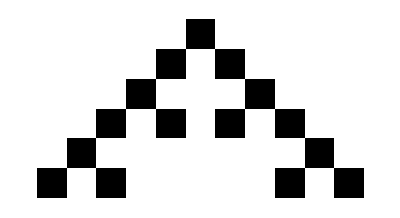

```mathematica
ArrayPlot[ca1]
```

## 2.Entender o conceito de Second-order rules, definidas como: o próximo estado s¬i no tempo t+1 é função não só de (s¬i-1, s¬i, s¬i+1) no tempo t, mas também de (s¬i-1, s¬i, s¬i+1) no tempo t-1. Em seguida responda: quantas funções existem? OBS: A definição está na documentação da função CellularAutomaton.

```mathematica
(*Se temos um autômato celular binário,temos 2^3=8 configurações possíveis no tempo t para três células consecutivas e outras 8 configurações no tempo t-1,dando um total de 8*8=64 configurações diferentes para qualquer regra de segunda ordem.*)(*Para cada uma dessas 64 configurações,a célula i pode ter 2 estados possíveis no tempo t+1. Assim,existiriam 2^64 funções possíveis de segunda ordem para um autômato celular binário.*)
(*Inicializa a lista de estados*)
states={{1,0,1,1,0,0,1},{0,0,1,0,1,1,0}}
```

{{1,0,1,1,0,0,1},{0,0,1,0,1,1,0}}

5

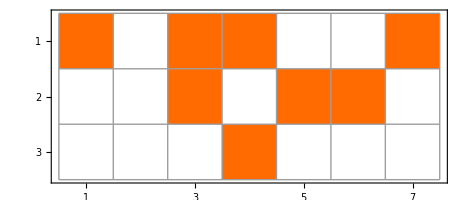

```mathematica
(*Define a regra de segunda ordem*)
secondOrderRule[previous_,current_]:=Module[{len=Length[current],next},next=Table[0,{len}];
For[i=2,i<len,i++,(*Exemplo de uma regra de segunda ordem simples:uma célula será 1 se a célula anterior estiver no estado 1 no tempo t e t-1,e a célula atual estiver no estado 0 no tempo t.*)If[previous[[i-1]]==1&&current[[i-1]]==1&&current[[i]]==0,next[[i]]=1]];
AppendTo[states,next];
next]

(*Executa a regra de segunda ordem para um número de passos*)
numberOfSteps=5
For[i=2,i<=numberOfSteps,i++,secondOrderRule[states[[i]],states[[i]]];]
(*Plota o resultado*)MatrixPlot[states,Mesh->True]
```

Neste exemplo, inicializamos um autômato celular de 7 células com dois estados iniciais diferentes. Então, definimos uma função secondOrderRule que aplica uma regra de segunda ordem específica para gerar o próximo estado baseado nos dois estados anteriores. A função secondOrderRule é então aplicada por um número de passos, e os resultados são visualizados com MatrixPlot.

## 3.Entender o conceito de regras confinadas (Captive) e analisar sua ocorrência no espaço elementar (i.e., quantas e quais são as regras?). OBS: A definição se encontra no CAMat.nb.

### Um Autômato Celular (CA) é considerado “Captive” quando todos os estados de transição são confinados ao conjunto de estados da vizinhança. Em outras palavras, o novo estado de uma célula deve ser um dos estados das células na vizinhança no tempo anterior.

```mathematica
(*Com base nesta definição e no código fornecido,podemos analisar todas as 256 regras elementares para determinar quais são "Captive".Para regras elementares em um autômato celular binário,k=2 e r=1,sendo k o número de estados possíveis para uma célula e r o raio da vizinhança. Portanto,vamos analisar regras com vizinhança de três células,onde cada célula pode estar no estado 0 ou 1.*)
RuleTableFromKAry[kAryRuleTable_,k_Integer:2,r_:1]:=
MapThread[
List[#1,#2]&,
{Tuples[Range[k-1,0,-1],⌊2r+1⌋],kAryRuleTable}];
```

```mathematica
RuleTable[rnum_Integer,k_Integer:2,r_:1]:=RuleTableFromKAry[PadLeft[IntegerDigits[rnum,k],k^(⌈2r⌉+1)],k,r];
```

```mathematica
CaptiveQ[rnum_Integer,k_Integer:2,r_:1]:=If[MemberQ[MemberQ[#[[1]],#[[2]]]&/@RuleTable[rnum,k,r],False],False,True];
```

```mathematica
(*Definição de CaptiveQ*)CaptiveQ[rnum_Integer,k_Integer:2,r_:1]:=If[MemberQ[MemberQ[#[[1]],#[[2]]]&/@RuleTable[rnum,k,r],False],False,True];
```

```mathematica
(*Lista de todas as regras elementares*)
elementaryRules=Range[0,255];
```

```mathematica
(*Filtrar regras que são "Captive"*)
captiveRules=Select[elementaryRules,CaptiveQ];
```

```mathematica
(*Mostra as regras "Captive"*)
captiveRules
```

{128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254}

Regras confinadas (ou “Captive”) em autômatos celulares são aquelas em que as transições de estado de uma célula devem respeitar uma condição específica: o estado futuro da célula deve ser um dos estados presentes na sua vizinhança. Isto é, se considerarmos uma célula e suas células vizinhas, o próximo estado da célula central deve obrigatoriamente ser um dos estados das células na sua vizinhança no tempo t.
Após rodar o código que filtra as regras “Captive” do conjunto de todas as regras elementares possíveis (0 a 255), foram encontradas várias regras que satisfazem a condição “Captive”. As regras que são “Captive” dentro do espaço elementar são:
{128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254}
Isso significa que, no contexto de autômatos celulares binários (onde cada célula tem 2 estados possíveis, 0 ou 1) e no espaço de regras elementares (regras 0 a 255), essas são as regras que seguem o critério de serem “Captive”, ou seja, o estado seguinte de cada célula é sempre um dos estados presentes em sua vizinhança no tempo anterior.

## 4.Entender o conceito de regras com um estado de espalhamento (Spreading) e analisar sua ocorrência nos espaços elementar e de raio 1.5. OBS: A definição se encontra no CAMat.nb.

### O conceito de um estado de espalhamento (Spreading State) em Autômatos Celulares refere-se a uma configuração em que um estado específico, denominado estado de espalhamento, tem a propriedade de se propagar pela vizinhança quando presente, e não pode ser o resultado de uma transição de estado quando ausente.

```mathematica
RuleTablePartitioned[rnum_Integer,k_Integer:2,r_:1]:={#[[1]]&/@#,#[[1,2]]}&/@Reverse[SortBy[GatherBy[RuleTable[rnum,k,r],#[[2]]&],#[[1,-1]]&]];
```

```mathematica
SpreadingStateQ[rnum_Integer,k_Integer:2,r_:1]:=
MemberQ[Module[{outState=#[[2]]},
{Union[MemberQ[#,outState]&/@#[[1]]],
Union[¬MemberQ[#,outState]&/@Complement[Tuples[Range[0,k-1],⌊2r+1⌋],#[[1]]]]}]&
/@RuleTablePartitioned[rnum,k,r],{{True},{True}}];
```

```mathematica
SpreadingState[rnum_Integer,k_Integer:2,r_:1]:=
Module[{pos=Position[Module[{outState=#[[2]]},
{
Union[MemberQ[#,outState]&/@#[[1]]],
Union[¬MemberQ[#,outState]&/@Complement[Tuples[Range[0,k-1],⌊2r+1⌋],#[[1]]]]
}]&/@Reverse@RuleTablePartitioned[rnum,k,r],{{True},{True}}]},
If[pos!={},pos[[1,1]]-1,{}]];
(*Verificar a existência de um estado de espalhamento na regra 128*)
SpreadingStateQ[128] (*Retorna:True*)
(*Verificar a existência de um estado de espalhamento na regra 127*)
SpreadingStateQ[127] (*Retorna:False*)
(*Verificar a existência de um estado de espalhamento na regra 19485 com k=3 e r=0.5*)
SpreadingStateQ[19485,3,0.5] (*Retorna:True*)
(*Encontrar a posição do estado de espalhamento para a regra 128*)
SpreadingState[128]
(*Se retornar n,isso significa que o n-ésimo elemento da tabela de regras é um estado de espalhamento*)
```

True

False

True

0

```mathematica
(*Analisar estados de espalhamento no espaço elementar*)
(*Para o espaço de raio 1.5, é necessário determinar o conjunto de regras apropriado com base em k e r,e então aplicar uma abordagem semelhante*)
elementarySpreadingStates=Select[Range[0,255],SpreadingStateQ]
```

{128,254}